```mathematica
DateString[]
$Version
<<SymbolicComputing`
$SCVersion
```

## References

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

## 9.5 Predator-Prey Equations

```mathematica
{ⅆx/ⅆt==a x-α x y,ⅆy/ⅆt==-c y+γ x y}
SCMAF[%,Factor,{At[All,2]},
SCFactor,{c-x γ,-1},PostAll->SCRemUnity](*5.1*)
```

{ⅆx/ⅆt==a x-x y α,ⅆy/ⅆt==-c y+x y γ}

{ⅆx/ⅆt==x (a-y α),ⅆy/ⅆt==-y (c-x γ)}

{ⅆx/ⅆt==x (a-y α),ⅆy/ⅆt==y (-c+x γ)}

#### Example 1

```mathematica
{ⅆx/ⅆt==x (a-y α),ⅆy/ⅆt==y (-c+x γ)}/.{a->1,α->0.5,c->0.75,γ->0.25}(*5.2*)
```

{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}

```mathematica
{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}
SCMAF[%,RA,{All,{ⅆx/ⅆt==0,ⅆy/ⅆt==0}},
SCSolve,{All,{x,y}},,
Thread,{All,Equal},Level->{1},
Thread,{All,Equal},IgnoreError->True]
```

{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x==0.,y==0.},{x==3.,y==2.}}

{{x,y}=={0.,0.},{x,y}=={3.,2.}}

{{x,y},{x,y}}=={{0.,0.},{3.,2.}}

{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}

{ⅆx/ⅆt,ⅆy/ⅆt}=={x (1-0.5 y),(-0.75+0.25 x) y}

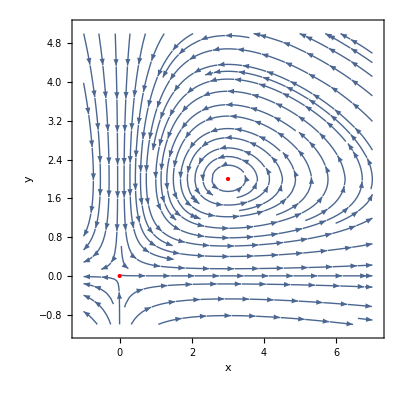

```mathematica
{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}(*5.2*)
SCMAF[%,Thread,{All,Equal},
StreamPlot,{At[2],{x,-1,7},{y,-1,5},FrameLabel->{x,y},Epilog->{Red,PointSize[Large],Point[{{0.,0.},{3.,2.}}]}},Take->{2}]
```

Examine the local behavior of solution near each critical point.

```mathematica
J==({{(∂F)/(∂x), (∂F)/(∂y)}, {(∂G)/(∂x), (∂G)/(∂y)}})
SCMAF[%,RA,{At[2],{F==x (1-0.5 y),G==(-0.75+0.25 x) y}},Post->SCEvalDeriv,MatrixForm->True]
```

J=={{(∂F)/(∂x),(∂F)/(∂y)},{(∂G)/(∂x),(∂G)/(∂y)}}

J==(1-0.5 y | -0.5 x
0.25 y | -0.75+0.25 x)

(x,y)=(0,0)

```mathematica
J==({{1-0.5 y, -0.5 x}, {0.25 y, -0.75+0.25 x}})
SCMAF[%,RA,{At[2],{x==0,y==0}},MatrixForm->True]
```

J=={{1-0.5 y,-0.5 x},{0.25 y,-0.75+0.25 x}}

J==(1. | 0.
0. | -0.75)

```mathematica
Eigensystem[({{1., 0.}, {0., -0.75}})]
```

{{1.,-0.75},{{-1.,0.},{0.,-1.}}}

```mathematica
{x,y}==Subscript[c, 1] Subscript[ξ, 1] ⅇ^(Subscript[r, 1] t)+Subscript[c, 2] Subscript[ξ, 2] ⅇ^(Subscript[r, 2] t)
SCMAF[%,RA,{At[2],{Subscript[r, 1]==1,Subscript[r, 2]==-0.75,Subscript[ξ, 1]=={-1.,0.},Subscript[ξ, 2]=={0.,-1.}}}]
```

{x,y}==ⅇ^(t r_1) c_1 ξ_1+ⅇ^(t r_2) c_2 ξ_2

{x,y}=={0.-1. ⅇ^t c_1,0.-1. ⅇ^(-0.75 t) c_2}

(x,y)=(3,2)

```mathematica
J==({{1-0.5 y, -0.5 x}, {0.25 y, -0.75+0.25 x}})
SCMAF[%,RA,{At[2],{x==3.,y==2.}},MatrixForm->True]
```

J=={{1-0.5 y,-0.5 x},{0.25 y,-0.75+0.25 x}}

J==(0. | -1.5
0.5 | 0.)

```mathematica
Eigensystem[({{0., -1.5}, {0.5, 0.}})]//Chop
```

{{0.+0.866025 ⅈ,0.-0.866025 ⅈ},{{-0.866025,0.+0.5 ⅈ},{-0.866025,0.-0.5 ⅈ}}}

```mathematica
{x,y}==Subscript[c, 1] Subscript[ξ, 1] ⅇ^(Subscript[r, 1] t)+Subscript[c, 2] Subscript[ξ, 2] ⅇ^(Subscript[r, 2] t)
SCMAF[%,RA,{At[2],{Subscript[r, 1]==0.866025 ⅈ,Subscript[r, 2]==-0.866025 ⅈ,Subscript[ξ, 1]=={-0.866025,0.5ⅈ},Subscript[ξ, 2]=={-0.866025,-0.5ⅈ}}},Post->ComplexExpand,
Chop,{At[2]}]
```

{x,y}==ⅇ^(t r_1) c_1 ξ_1+ⅇ^(t r_2) c_2 ξ_2

{x,y}=={0.-0.866025 Cos[0.+0.866025 t] c_1-0.866025 Cos[0.-0.866025 t] c_2+ⅈ (0.-0.866025 Sin[0.+0.866025 t] c_1-0.866025 Sin[0.-0.866025 t] c_2),0.-0.5 Sin[0.+0.866025 t] c_1+0.5 Sin[0.-0.866025 t] c_2+ⅈ (0.+0.5 Cos[0.+0.866025 t] c_1-0.5 Cos[0.-0.866025 t] c_2)}

{x,y}=={-0.866025 Cos[0.866025 t] c_1-0.866025 Cos[0.866025 t] c_2+ⅈ (-0.866025 Sin[0.866025 t] c_1+0.866025 Sin[0.866025 t] c_2),-0.5 Sin[0.866025 t] c_1-0.5 Sin[0.866025 t] c_2+ⅈ (0.5 Cos[0.866025 t] c_1-0.5 Cos[0.866025 t] c_2)}

Find the trajectories

```mathematica
SCAFE[ⅆy/ⅆx,SCTransDeriv,{All,TransVar->{x,t}},
RA,{At[2],ⅆt/ⅆx->(ⅆx/ⅆt)^-1},
RA,{At[2],{ⅆx/ⅆt==x(1-0.5y),ⅆy/ⅆt==y(-0.75+0.25x)}},PostAll->SCDerivToFrac,
SCMultEq,{All,(1-0.5 y)/y ⅆx},Post->SCDiffToInt,
SCEvalInt,{All,ReplConst->{C,0}},
SCSolve,{All,C},Post->Reverse,
ExpandAll,At[1]](*5.13*)
```

ⅆy/ⅆx==ⅆt/ⅆx ⅆy/ⅆt

-1. (0.25 x+0.5 y-0.75 Log[x]-Log[y])==C

-0.25 x-0.5 y+0.75 Log[x]+1. Log[y]==C

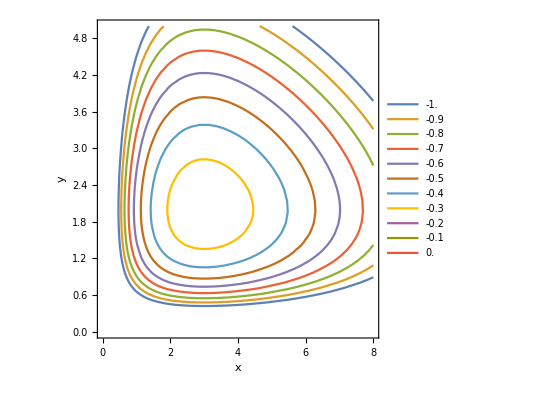

```mathematica
ContourPlot[Evaluate@Table[-0.25 x-0.5 y+0.75 Log[x]+1. Log[y]==C,{C,-1,0,0.1}],{x,0,8},{y,0,5},FrameLabel->{x,y},PlotLegends->Table[C,{C,-1,0,0.1}]]
```

{ⅆx/ⅆt==x (1-0.5 y),ⅆy/ⅆt==(-0.75+0.25 x) y}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

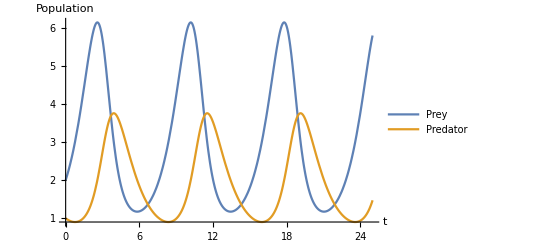

```mathematica
{ⅆx/ⅆt==x(1-0.5y),ⅆy/ⅆt==y(-0.75+0.25x)}
SCMAF[%,RA,{All,{x->x[t],y->y[t]}},Post->SCEvalDeriv,
Join,{All,{x[0]==2,y[0]==1}},
NDSolve,{All,{x,y},{t,0,25}},Take->{1},
{x[t],y[t]}/.#&,All,
Plot,{All,{t,0,25},AxesLabel->{t,Population},PlotLegends->{Prey,Predator}}]
```